# Reverse Dictionary

## Data

Data was taken from the site of the following paper: Hill, F. Cho, KH., Korhonen, A., and Bengio, Y. Learning to Understand Phrases by Embedding the Dictionary. 2016. Transactions of the Association for Computational Linguistics (TACL). Originally it was recollected via WordNik API in Python.

## Proof of Concept

For this first proof of concept analysis, we used 50 of the most common nouns in the English language. We chose the 50 with more definitions assigned to them so that the training can be more efficient. The number of definitions per word was normalized to the minimum among the maximum number of definitions for each word. This was so there would be no bias in the data.

Global Set

```mathematica
rawData=Import["Personal\\WSS\\wss_project\\training_data\\60Def50Words.csv"];
```

```mathematica
associate[elem_]:=Last[elem]-> First[elem];
```

```mathematica
wordDefSet=Map[associate, rawData];
RandomSample[wordDefSet, 10]//TableForm
```

one appointed or elected to preside over an organized body of people such as an assembly or meeting→president
 to become day dawn same as daw→day
 a purpose goal or aim→end
 have no words for to be unable to describe or talk about→word
 to make horizontal flat or even leveled the driveway with a roller leveled off the hedges with the clippers→level
 by reason of because of→reason
 a human or an adult male human belonging to a specific occupation group nationality or other category→man
 a film or membrane which is developed on the surface of fermented alcoholic liquids such as vinegar wine etc and acts as a means of conveying the oxygen of the air to the alcohol and other combustible principles of the liquid thus leading to their oxidation→mother
 a striking example→mother
 a sequence of digits and letters used to register people automobiles and various other items→number

```mathematica
wordset=DeleteDuplicates[Map[Last,wordDefSet]];
```

Testing Set

```mathematica
simpleTestingSet=Select[Normal[DeleteDuplicates[Association[RandomSample[wordDefSet]]]],Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[simpleTestingSet, 10]//TableForm
```

the whole people of one body politic the commonwealth usually with the definite article in a particular sense a civil and self governing community a commonwealth→state
 a part that supports or strengthens from the rear the back of a couch→back
 rotational period of a planet especially earth→day
 a succesion or substitution of one thing in the place of another a difference novelty variety→change
 to be a gay companion→company
 the title by which any person or thing is known or designated a distinctive specific appellation whether of an individual or a class→name
 a set of dishes or utensils a silver tea service→service
 a relative degree as of achievement intensity or concentration an unsafe level of toxicity a high level of frustration→level
 it is not a place to live that can be easily packed up and carried away like a tent or moved like a caravan→house
 primary leader of a corporation→president

Training Set

```mathematica
simpleTrainingSet=Select[wordDefSet,Not[MemberQ[simpleTestingSet,First[#]->_]]&&Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[simpleTrainingSet, 10]//TableForm
```

the moving load carrying component of an elevator or other cable drawn transport mechanism→car
 companionship→company
 to list or register in or as if in a book→book
 the probability that a statistical test will reject the null hypothesis when the alternative hypothesis is true→power
 to drive force→job
 divided in part→party
 those of a certain name a race a family→name
 to have sexual intercourse→company
 his salary is a year→president
 imaginary or unreal the guy had just hit it big→air

Simplest Approach

Simplest Approach consists of using built in function Classify to attempt to solve the problem.

```mathematica
classifier=Classify[simpleTrainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
cm=ClassifierMeasurements[classifier,simpleTestingSet]
```

ClassifierMeasurementsObject[…]

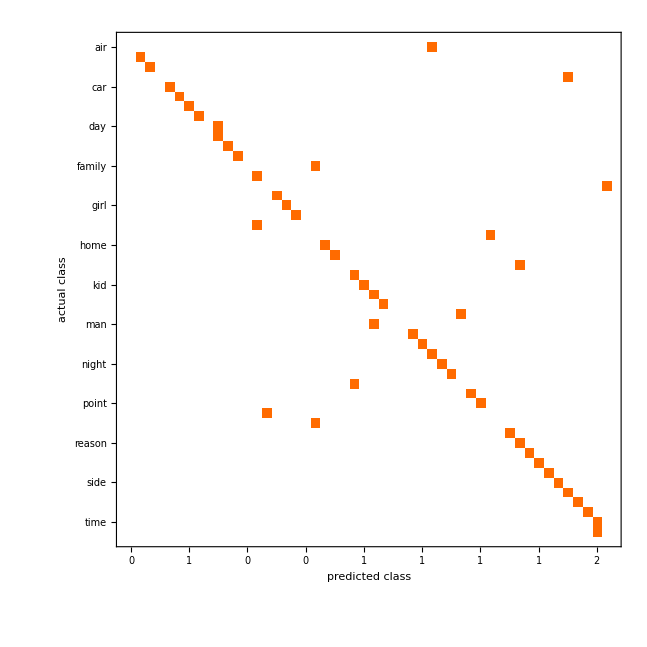

```mathematica
cm["ConfusionMatrixPlot"]
```

```mathematica
ClassifierInformation[classifier]
```

Classifier information
Method | Markov
Number of classes | 50
Number of features | 1
Number of training examples | 2939
Number of tokens | 5687
Markov order | 1
Regularization method | Katz

Apparently this does it, and the performance seems pretty good. Now, this model might be over-fitted, so we must test with data it has never seen.

```mathematica
ClassifierMeasurements[classifier,simpleTestingSet,"Accuracy"]
```

0.72

```mathematica
ClassifierMeasurements[classifier,simpleTestingSet,"F1Score"]
```

<|air→0.,back→1.,book→1.,business→0.,car→1.,case→1.,change→1.,company→1.,day→0.,end→0.666667,eye→1.,face→1.,family→0.,father→0.666667,force→0.,game→1.,girl→1.,group→1.,hand→0.,head→0.,home→1.,house→1.,issue→0.,job→0.666667,kid→1.,law→0.666667,level→1.,lot→0.,man→0.,minute→1.,mother→1.,name→0.666667,night→1.,number→1.,part→0.,party→1.,point→1.,power→0.,president→0.,question→1.,reason→0.666667,right→1.,school→1.,service→1.,side→1.,state→0.666667,study→1.,thing→1.,time→0.666667,word→0.|>

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@classifier[text,"TopProbabilities"->3]]
```

## Complete Data Set

Now that we have a working version, we can attempt to scale things up by training our model with all the data available.

Training Set

```mathematica
rawData=Import["Personal\\WSS\\wss_project\\training_data\\training_data.csv"];
```

Lets filter just for nouns.

```mathematica
nouns=WordList["Noun"];
```

```mathematica
filtered=Select[rawData,MemberQ[nouns,First[#]]&];
RandomSample[filtered,10]
```

{{fawn, to exhibit affection or attempt to please as a dog does by wagging its tail whining or cringing},{fawn, to seek favor or attention by flattery and obsequious behavior},{fawn, a young deer especially one less than a year old},{fawn, a grayish yellow brown to moderate reddish brown},425326,{jawbone, any bone of the jaws as a maxillary or mandibular bone especially a bone of the lower jaw},{jawbone, talk idly or casually and in a friendly way},{jawbone, the jaw in vertebrates that is hinged to open the mouth}}
 |  |  |  |

Lets look at the frequency of each word, as well as the average.

```mathematica
freq=Reverse[SortBy[Tally[First[#]&/@filtered],Last]];
freq[[;;10]]
```

{{go,603},{stick,412},{fall,412},{base,398},{clear,382},{do,360},{rest,344},{hang,344},{crown,342},{jacks,336}}

```mathematica
avgFreq=N[Total[Last[#]&/@freq]/Length[freq]]
```

20.431

```mathematica
trainingSet=Map[associate, filtered];
RandomSample[trainingSet,10]//TableForm
```

a solemn form of supplication in the public worship of various churches in which the clergy and congregation join the former leading and the latter responding in alternate sentences→litany
 a sensation experienced in touching something with a characteristic texture felt the touch of snowflakes on her face→touch
 technically in law the person upon whom the law casts an estate in real property immediately on the death of the ancestor as distinguished from one who takes by will as a legatee or devisee and from one who succeeds by law to personal property as next of kin→heir
 the quality or condition of being perfect→perfection
 a vain foolish or incongruous fancy or creature of the imagination as the chimera of an author→chimera
 a ceremonial object used in puebloan kachina cults that resembles a euro american masks→masking
 it was formed by cutting the stem of the plant into thin longitudinal slices which were gummed together and pressed→papyrus
 the act of disbanding→disbandment
 hence food placed on a table to be partaken of fare entertainment→table
 same as bath→bat

```mathematica
Length[trainingSet]
```

425333

```mathematica
wordset=DeleteDuplicates[Map[Last,trainingSet]];
Length[wordset]
```

20818

Testing Set

```mathematica
rawTesting=Import["Personal\\WSS\\wss_project\\test_data\\testing_data.csv"];
```

```mathematica
filteredTest=Select[rawTesting,MemberQ[nouns,First[#]]&];
```

```mathematica
testingSet=Map[associate, filteredTest];
RandomSample[testingSet, 10]//TableForm
```

the limbs that birds move in order to fly→wing
 a strong emotional feeling of physical or mental attraction towards somebody→love
 thin strands of living tissue that grow out of the skin of animals for warmth→hair
 a journey in an aeroplane or the act of travelling in the air→flight
 to touch someone or something with an extended finger or long thin object→poke
 a flat piece of material you put on your bed or the ground for warmth or comfort→blanket
 computer or mobile phone→screen
 somebody who controls an organisation or group of people→leader
 a clear material that you can see through used to make windows→glass
 an agenda for a whole year that includes a particular part or page for each month→calendar

Simplest Approach

As it proved to be working for the small dataset, we can try again with Classify.

```mathematica
cl=Classify[trainingSet,PerformanceGoal->"Quality"]
```

Classify::bdfmt: Argument filtered should be a rule, a list of rules, or an association.

Classify[filtered,PerformanceGoal→Quality]

```mathematica
ClassifierInformation[cl,"TrainingTime"]
```

3954.02 s

```mathematica
ClassifierMeasurements[cl,testingSet,"Accuracy"]
```

0.

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@cl[text,"TopProbabilities"->10]]
```

## Playing with variance and performance

Lets look at the whole data set.

```mathematica
completeDataFreq=Reverse[SortBy[Tally[First[#]&/@rawData],Last]];
completeDataFreq[[;;10]]
```

{{var,648},{go,603},{nox,474},{points,438},{rounds,424},{stick,412},{fall,412},{bak,408},{det,404},{base,398}}

```mathematica
Length[completeDataFreq]
```

67713

```mathematica
completeDataMean=N[Mean[Last[#]&/@completeDataFreq]]
```

12.5895

```mathematica
completeDataVar=N[Variance[Last[#]&/@completeDataFreq]]
```

430.875

Filtering for nouns.

```mathematica
Length[freq]
```

20818

```mathematica
filteredMean=N[Mean[Last[#]&/@freq]]
```

20.431

```mathematica
filteredVar=N[Variance[Last[#]&/@freq]]
```

759.839

Variance grew, so this means that the performance of our classifier might worsen.

We can try to balance things by taking only words that satisfy having more than a certain number of definitions.

```mathematica
getBalancedList[noElem_]:=Module[{wordSet,wordCounter,resultList,elem,word},(
	wordSet=First[#]&/@Select[freq,Last[#]≥noElem&];
	wordCounter=<||>;
	resultList={};
	For[i=1,i≤Length[filtered],i++,
		elem=filtered[[i]];
		word=First[elem];
		If[MemberQ[wordSet,word],
			If[KeyExistsQ[wordCounter,word],
				If[wordCounter[[word]]≤noElem,
					AppendTo[resultList,elem];
					wordCounter[[word]]+=1],
			AppendTo[wordCounter,word->1]
			]
		]
	];
	resultList
)]
```

```mathematica
balanced=getBalancedList[35];
RandomSample[balanced,10]
```

{{sprouting, the molten silver beneath the thin solid crust forces up the crust with explosive violence and a part of it solidifies in the form of trees or sprouts},{hire, informal one who is hired two new hires in the sales department},{proposition, propositions de necessario simpliciter or categorical apodictic propositions},{engraving, bewick established the ascendancy of the white line that is the incision made by the engravers tools},{bubble, to cry weep},{nay, no all but four democrats voted nay},{normal, mathematics being at right angles perpendicular},{signal, to give a signal or signals make communication by signals},{brown, to give a bright brown color to as to gun barrels by forming a thin coat of oxide on their surface},{clearance, the amount of space or distance by which a moving object clears something}}

```mathematica
Length[balanced]
```

104741

```mathematica
wordset=DeleteDuplicates[Map[First,balanced]];
balancedWordDef=Map[associate, balanced];
```

Testing set

```mathematica
filteredTest=Select[rawTesting,MemberQ[balancedWords,First[#]]&];
```

```mathematica
balTestingSet=Select[Normal[DeleteDuplicates[Association[RandomSample[balancedWordDef]]]],Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[testingSet, 10]//TableForm
```

the desire to improve your life or to achieve better things in your career→ambition
 a feeling of pain in the head or brain→headache
 a competition where people try to reach a place in the quickest possible time→race
 a group of men who fight together in the name of a country→army
 a machine for taking photographs→camera
 a clear material that you can see through used to make windows→glass
 a part of a house or building where cars can park indoors→garage
 the circular parts of cars or vehicles designed to roll along the ground→wheel
 another word for hair that is used when the hair is on an animal→fur
 the sweet liquid stored inside fruit that is healthy and delicious to drink→juice

Training set

```mathematica
balTrainingSet=Select[balancedWordDef,Not[MemberQ[balTestingSet,First[#]->_]]&&Not[StringContainsQ[Last[#],"ï»¿"]]&];
RandomSample[trainingSet,10]//TableForm
```

to hit someone or something→belt
 a support on which things can be put→rest
 a waste pipe that carries away sewage or surface water→cloaca
 the characteristic of being newsworthy→newsworthiness
 an aphidian a plant louse a member of the genus aphis or family aphididÅ.93ce which see→aphid
 being under the power or sovereignty of another or others→dependent
 a person who diets usually in an effort to lose weight→dieter
 harshly ironic or sinister→mordant
 a racial religious political national or other group thought to be different from the larger group of which it is part→minority
 to cause to break from internal pressure→burst

```mathematica
Length[balTrainingSet]
```

100581

```mathematica
wordset=DeleteDuplicates[Map[Last,balTrainingSet]];
Length[wordset]
```

2996

Classify

Lets classify with this balanced data set.

```mathematica
clssfy=Classify[balTrainingSet,PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[clssfy,"TrainingTime"]
```

133.662 s

```mathematica
ClassifierMeasurements[clssfy,balTestingSet,"Accuracy"]
```

0.0524032

```mathematica
ClassifierInformation[clssfy]
```

Classifier information
Method | Markov
Number of classes | 2996
Number of features | 1
Number of training examples | 100581
Number of tokens | 37602
Order | 0

Test with own definitions

```mathematica
text="";
InputField[Dynamic[text],String,ContinuousAction->True]
```

```mathematica
Dynamic[Column@cl[text,"TopProbabilities"->10]]
```